## Disk

```mathematica
p[r_,θ_]:= (1-r^2)/(1-2 r Cos[θ] + r^2)
```

```mathematica
TabView[{
"3D"->ParametricPlot3D[{r Cos[θ],r Sin[θ],p[r,θ]},{r,0,0.9},{θ,0, 2π}],
"r=1^-"->Plot[p[0.99,θ],{θ,0, 4π}],
"θ=0"->Plot[p[r,0],{r,0,1}]
}]
```

123

```mathematica
NIntegrate[p[r,θ],{r,0,1},{θ,0, 2π}]
```

6.28319

```mathematica
Clear[θ,r,ρ,ϕ,u0]
u0[θ_]:=0.1 Cos[θ]-0.3 Sin[2 θ]
u[r_,θ_]:=1/(2π)NIntegrate[ p[r,θ-ϕ]*u0[ϕ],{ϕ,0, 2π}]
AbsoluteTiming[u[0.2,0.3]]
```

{0.0053932,0.012331}

```mathematica
ParametricPlot3D[{r Cos[θ],r Sin[θ],u[r,θ]},{r,0,0.9},{θ,0, 2π},
MaxRecursion->0]
```

## FS Demo

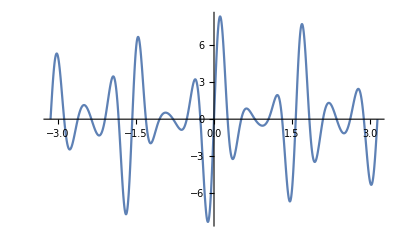

{0.0141793,0.000725138}

{0.0142431,0.}

```mathematica
f[θ_] := Exp[Cos[4θ]+ArcTan[ Cos[3 θ]+ 2 Cos[Sin[2 θ]]]]
Plot[f[θ], {θ, -4 π, 4 π}];
Plot[ f[θ] Sin[12 θ],{θ,-π,π}]
a[n_]:= NIntegrate[f[θ] Cos[n θ],{θ,-π,π}]
b[n_]:= NIntegrate[f[θ] Sin[n θ],{θ,-π,π}]
AbsoluteTiming[a[24]]
AbsoluteTiming[b[24]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.150275}. NIntegrate obtained 3.9124×10^-11 and 3.81411×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.150275}. NIntegrate obtained -7.81215×10^-11 and 5.18537×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.150275}. NIntegrate obtained -6.01449×10^-12 and 4.12799×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

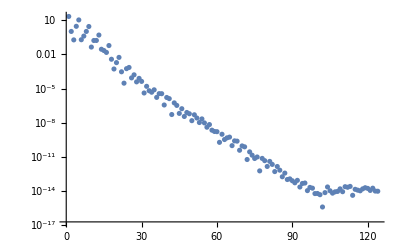

```mathematica
ListLogPlot[Abs[Table[a[n],{n, 0, 123}]]]
```